```mathematica
link=Install[LinkConnect["44021@192.168.150.128,41327@192.168.150.128",LinkProtocol->"TCPIP"]]
```

LinkObject[…]

```mathematica
handle = With[
{c=15,Ωp=1.0,Ωe=-100,θr=0.45,θe=Sqrt[0.8],θb=0.045,ωb=14.2302,ωe=150,
ωp ={0.039893,0.143882,0.348679,0.597894,0.815419,0.984766,1.11653,1.21888,1.29599,1.34998,1.38201,1.39263,1.38201,1.34998,1.29599,1.21888,1.11653,0.984766,0.815419,0.597894,0.348679,0.143882,0.039893},
vd={1.90288,1.99424,2.025,1.99424,1.90288,1.7537,1.55124,1.30164,1.0125,0.692591,0.351638,0,-0.351638,-0.692591,-1.0125,-1.30164,-1.55124,-1.7537,-1.90288,-1.99424,-2.025,-1.99424,-1.90288},
vr={-0.692591,-0.351638,0,0.351638,0.692591,1.0125,1.30164,1.55124,1.7537,1.90288,1.99424,2.025,1.99424,1.90288,1.7537,1.55124,1.30164,1.0125,0.692591,0.351638,0,-0.351638,-0.692591}
},
dist=Join[
Thread[wstpDRingDistribution[Ωp,ωp,θr,θr,vd,vr]],
Thread[wstpDMaxwellianDistribution[{Ωp,Ωe},{ωb,ωe},{θb,θe}]]];
wstpDCreateDispersionObject[c,dist]];
```

```mathematica
sol=With[{k=5.08,wna=84.2Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[5.0,0.047] (1+0.0001 I {0,1,2}),MaxIterations->100]];
```

{3.90174-0.0142553 ⅈ,3.89761-0.0130219 ⅈ,3.89358-0.0119131 ⅈ,3.88966-0.0109059 ⅈ,3.88583-0.00997506 ⅈ,3.88211-0.00909418 ⅈ,3.8785-0.00823671 ⅈ,3.87498-0.00736825 ⅈ,3.87158-0.0064431 ⅈ,3.86829-0.00542556 ⅈ,3.86512-0.00427602 ⅈ,3.86208-0.00294439 ⅈ,3.85921-0.0013664 ⅈ,3.85652+0.000527488 ⅈ,3.85408+0.00282902 ⅈ,3.85198+0.00565489 ⅈ,3.85037+0.00914261 ⅈ,3.84949+0.013446 ⅈ,3.84978+0.0186925 ⅈ,3.85188+0.0248447 ⅈ,3.85662+0.0314632 ⅈ}

{3.90174-0.0142553 ⅈ,3.89761-0.0130219 ⅈ,3.89358-0.0119131 ⅈ,3.88966-0.0109059 ⅈ,3.88583-0.00997506 ⅈ,3.88211-0.00909418 ⅈ,3.8785-0.00823671 ⅈ,3.87498-0.00736825 ⅈ,3.87158-0.0064431 ⅈ,3.86829-0.00542556 ⅈ,3.86512-0.00427602 ⅈ,3.86208-0.00294439 ⅈ,3.85921-0.0013664 ⅈ,3.85652+0.000527488 ⅈ,3.85408+0.00282902 ⅈ,3.85198+0.00565489 ⅈ,3.85037+0.00914261 ⅈ,3.84949+0.013446 ⅈ,3.84978+0.0186925 ⅈ,3.85188+0.0248447 ⅈ,3.85662+0.0314632 ⅈ,3.86457+0.0375796 ⅈ,3.87575+0.0420651 ⅈ,3.88984+0.0441347 ⅈ,3.90669+0.0434672 ⅈ,3.92674+0.0402339 ⅈ,3.951+0.035787 ⅈ,3.97882+0.0331168 ⅈ,4.00715+0.0331838 ⅈ,4.03435+0.0348232 ⅈ,4.05986+0.0371255 ⅈ,4.08334+0.0392436 ⅈ,4.10484+0.0403314 ⅈ,4.12466+0.0398896 ⅈ,4.143+0.0377132 ⅈ,4.15986+0.0337452 ⅈ,4.17504+0.0280582 ⅈ,4.19949+0.010081 ⅈ,4.19918+0.012944 ⅈ,4.20791+0.00480551 ⅈ,4.21483-0.00289897 ⅈ}

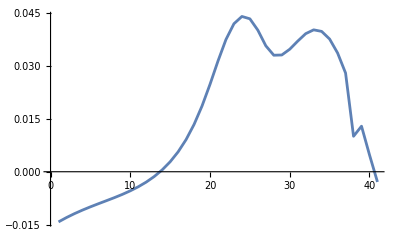

```mathematica
sol1=With[{k=Range[4.5,3.5,-0.05],wna=88.6Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[3.85,0.031] (1+0.0001 I {0,1,2}),MaxIterations->100]];
sol2=With[{k=Range[4.55,5.5,0.05],wna=88.6Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[3.85,0.031] (1+0.0001 I {0,1,2}),MaxIterations->100]];
sol1=Reverse[sol1[[2,2]]]
sol=Join[sol1,sol2[[2,2]]]
ListLinePlot[Im[sol]]
```

```mathematica
Export["origin87.csv",Im[sol]];

Export["re.csv",Re[sol]];
```